# Лр. 2. ГРАФИЧЕСКИЕ ЭЛЕМЕНТЫ НА ПЛОСКОСТИ: ПОЛИГОН

A. Shpak
Sun, 24-Sep-2023

## Section. Дополните систему kmGeom новым функционалом, позволяющим работать с объектом «полигон на плоскости».

### Section.Subsection. Напишите функцию, вычисляющую периметр произвольного полигона.

```mathematica
ClearAll[NamedQ,𝔨𝔪];
(** Атрибуты и описание **)
𝔨𝔪::usage="Knowledge base «computer mathematics»";
SetAttributes[𝔨𝔪,{Protected,ReadProtected}];
NamedQ::usage="Check: is there a name of tested equations";
NamedQ[n1_,n2__]:=And[NamedQ[n1],NamedQ[n2]];
SetAttributes[NamedQ,Listable];
```

```mathematica
ClearAll[kmPoint];
(** Атрибуты и описание **)
SetAttributes[kmPoint,ReadProtected];
kmPoint::usage="Point on the surface";
(** Свойства **)
NamedQ[kmPoint[𝔨𝔪,id_String,___]]^:=id≠"";
kmPoint[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
kmPoint[𝔨𝔪,id_String,___]["id"]:=If[id=="","Point",id];
(** Конструкторы **)
kmPoint[id_String,coord:{_,_}]:=kmPoint[𝔨𝔪,id,coord];
kmPoint[coord:{_,_}]:=kmPoint[𝔨𝔪,"",coord];
kmPoint[{L1_kmLine,L2_kmLine}]:=kmPoint[#[[2]]&/@(First@NSolve@Through[{L1,L2}@"equ"])]
(** Декораторы **)
Format[P_kmPoint,StandardForm]:=Row@{P["id"],"(",Row[P["coord"],","],")"};
```

```mathematica
ClearAll[kmVector];
(** Атрибуты и описание **)
SetAttributes[kmVector,ReadProtected];
kmVector::usage="Vector on the surface";
(** Свойства **)
NamedQ[kmVector[𝔨𝔪,id_String,___]]^:=id≠"";
kmVector[𝔨𝔪,id_String,___]["id"]:=If[id=="","Vector",id];
kmVector[𝔨𝔪,_String,coord_List,___]["coord"]:=coord;
(** Конструкторы **)
kmVector[id_String,coord_List]:=kmVector[𝔨𝔪,id,coord];
kmVector[coord_List]:=kmVector[𝔨𝔪,"",coord];
kmVector[id_String,P0_kmPoint,P1_kmPoint]:=kmVector[id,P1@"coord"-P0@"coord"];
kmVector[P0_kmPoint,P1_kmPoint]:=kmVector[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
MakeBoxes[V_kmVector,StandardForm]^:=TemplateBox[{V@"id",
RowBox@Riffle[MakeBoxes[#,StandardForm]&/@V["coord"],","]
},"Point2D",
DisplayFunction:>(RowBox@{OverscriptBox[#1,"⇀"],"(",#2,")"}&),
InterpretationFunction->(RowBox@{"{",#2,"}"}&),
Tooltip->Automatic];
```

```mathematica
ClearAll[kmLine];
(** Атрибуты и описание **)
SetAttributes[kmLine,ReadProtected];
kmLine::usage="Line on the surface";
(** Свойства **)
NamedQ[kmLine[𝔨𝔪,id_String,___]]^:=id≠"";
kmLine[𝔨𝔪,id_String,___]["id"]:=If[id=="","Line",id];
kmLine[𝔨𝔪,_String,coef_List,___]["coef"]:=coef;
kmLine[𝔨𝔪,_String,coef_List,___]["equ",vars:{_Symbol,_Symbol}:{x,y}]:=
coef.Append[vars,1]==0;
(** Конструкторы **)
kmLine[equ:(__==0),vars:{_Symbol,_Symbol}]:=kmLine["",equ,vars];
kmLine[id_String,A_. x_+B_.y_+C_.==0,{x_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{A,B,C}]/;¬PossibleZeroQ[Abs@A+Abs@B];
kmLine[id_String,A_. x_+C_.==0,{x_Symbol,_Symbol}]:=kmLine[𝔨𝔪,id,{A,0,C}];
kmLine[id_String,B_. y_+C_.==0,{_Symbol,y_Symbol}]:=kmLine[𝔨𝔪,id,{0,B,C}];
kmLine[id_String,P_kmPoint,Dir_kmVector]:=kmLine[𝔨𝔪,id,
Append[#,-#.P["coord"]]&[({{0, -1}, {1, 0}}).Dir["coord"]]];
kmLine[P_kmPoint,Dir_kmVector]:=kmLine[
If[NamedQ[P,Dir],StringJoin[P@"id",Dir@"id"],""],P,Dir];
kmLine[id_String,P1_kmPoint,P2_kmPoint]:=kmLine[id,P1,kmVector["",P1,P2]]
kmLine[{P1_kmPoint,P2_kmPoint}]:=kmLine[P1,kmVector[P2@"id",P1,P2]]
kmLine[id_String,segment_kmSegment]:=Block[{x1=segment["end1Coord"][[1]],y1=segment["end1Coord"][[2]],x2=segment["end2Coord"][[1]],y2=segment["end2Coord"][[2]]},kmLine[id,(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
kmLine[segment_kmSegment]:=Block[{x1=segment["end1Coord"][[1]],y1=segment["end1Coord"][[2]],x2=segment["end2Coord"][[1]],y2=segment["end2Coord"][[2]]},kmLine[(y1-y2)x+(x2-x1)y+(x1*y2-x2*y1)==0,{x,y}]]
(** Декораторы **)
Format[L_kmLine,StandardForm]:=Row@{L@"id",": ",L@"equ"};
```

```mathematica
ClearAll[getTwoLinePoints];
getTwoLinePoints[line_kmLine]:=Map[kmPoint,
If[Apply[Less,Abs@line["coef"]⟦{1,2}⟧],
Table[{x,y}/.First@Solve[line["coef"].{x,y,1}==0],{x,{-1,1}}],
Table[{x,y}/.First@Solve[line["coef"].{x,y,1}==0],{y,{-1,1}}]]]
```

```mathematica
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[
ReplaceAll[gp,{
P_kmPoint:>Tooltip[Point@P@"coord",Style[Format[P,StandardForm],Large]],
L_kmLine:>Tooltip[
InfiniteLine@Through@getTwoLinePoints[L]@"coord",
Style[Format[L,StandardForm],Large]]
}],
opts];
```

```mathematica
ClearAll[kmSegment];
(** Атрибуты и описание **)
SetAttributes[kmSegment,ReadProtected];
kmLine::usage="Отрезок на плоскости";
(** Свойства **)
NamedQ[kmSegment[𝔨𝔪,id_String,___]]^:=id≠"";
kmSegment[𝔨𝔪,id_String,___]["id"]:=If[id=="","Segment",id];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["coords"]:=kmPoint[#]&/@endCoords;
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end1Coord"]:=kmPoint[endCoords[[1]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["end2Coord"]:=kmPoint[endCoords[[2]]];
kmSegment[𝔨𝔪,id_String,endCoords:{{_,_},{_,_}}]["len"]:=Sqrt[Plus@@((endCoords[[1]]-endCoords[[2]])^2)]
(** Конструкторы **)
kmSegment[id_String,endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,id,endsCoords];
kmSegment[endsCoords:{{_,_},{_,_}}]:=kmSegment[𝔨𝔪,"",endsCoords];
kmSegment[id_String,P0_kmPoint,P1_kmPoint]:=kmSegment[id,{P1@"coord",P0@"coord"}];
kmSegment[P0_kmPoint,P1_kmPoint]:=kmSegment[
If[NamedQ[P0,P1],StringJoin[P0@"id",P1@"id"],""],P0,P1];
(** Декораторы **)
Format[Segment_kmSegment,StandardForm]:=Row@{Segment@"id",": ",Segment@"coords"};
(**Отображение отрезка на рисунке**)
ClearAll[kmGraphics2D];
kmGraphics2D[gp_List,opts___]:=Graphics[
ReplaceAll[gp,{
P_kmPoint:>Tooltip[Point@P@"coord",Style[Format[P,StandardForm],Large]],
L_kmLine:>Tooltip[
InfiniteLine@Through@getTwoLinePoints[L]@"coord",
Style[Format[L,StandardForm],Large]],
Segment_kmSegment:>Tooltip[Line[{Segment@"end1Coord",Segment@"end2Coord"}]]
}],
opts];
```

#### Функции для заданий

1.5

```mathematica
getParameter[Segment_kmSegment,P_kmPoint]:=Block[{x0=(getLeftSegmentPoint[Segment]["coord"])[[1]],x1=(getRightSegmentPoint[Segment]["coord"])[[1]]},(First@First@NSolve[(x1-x0)*t+x0==P["coord"][[1]],t])[[2]]]
```

```mathematica
getRightSegmentPoint[P1_kmPoint,P2_kmPoint]:=If[P1["coord"][[1]]>P2["coord"][[1]],P1,P2]
getRightSegmentPoint[Segment_kmSegment]:=Block[{coord1=Segment["end1Coord"],coord2=Segment["end2Coord"]},If[coord1[[1]]>coord2[[1]],kmPoint[coord1],kmPoint[coord2]]]
getLeftSegmentPoint[P1_kmPoint,P2_kmPoint]:=If[P1["coord"][[1]]<P2["coord"][[1]],P1,P2]
getLeftSegmentPoint[Segment_kmSegment]:=Block[{coord1=Segment["end1Coord"],coord2=Segment["end2Coord"]},If[coord1[[1]]<coord2[[1]],kmPoint[coord1],kmPoint[coord2]]]
```

```mathematica
getParametersOfIntersection[Segment1_kmSegment,Segment2_kmSegment]:=Block[{Line1=kmLine[Segment1],Line2=kmLine[Segment2]},res=getLinesIntersectionPoint[Line1,Line2];getParameter[#,res]&/@{Segment1,Segment2}]
```

```mathematica
ClearAll[kmPolygon];
(** Атрибуты и описание **)
SetAttributes[kmPolygon,ReadProtected];
kmPoint::usage="Polygon on the surface";
(** Свойства **)
NamedQ[kmPolygon[𝔨𝔪,id_String,___]]^:=id≠"";
kmPolygon[𝔨𝔪,_String,coordsOfPoints_List]["coordsOfPoints"]:=#["coord"]&/@coordsOfPoints;
kmPolygon[𝔨𝔪,_String,coordsOfPoints_List]["points"]:=coordsOfPoints;
kmPolygon[𝔨𝔪,_String,coordsOfPoints_List]["lineSegments"]:=Append[kmSegment[{coordsOfPoints[[#]]["coord"],coordsOfPoints[[#+1]]["coord"]}]&/@Range[Length[coordsOfPoints]-1],kmSegment[{coordsOfPoints[[Length[coordsOfPoints]]]["coord"],coordsOfPoints[[1]]["coord"]}]]
kmPolygon[𝔨𝔪,id_String,___]["id"]:=If[id=="","Polygon",id];
(** Конструкторы **)
kmPolygon[id_String,coordsOfPoints_List]:=If[ToString[Head[coordsOfPoints[[1]]]]=="kmPoint",kmPolygon[𝔨𝔪,id,coordsOfPoints],kmPolygon[𝔨𝔪,id,kmPoint[#]&/@coordsOfPoints]];
kmPolygon[coordsOfPoints_List]:=If[ToString[Head[coordsOfPoints[[1]]]]=="kmPoint",kmPolygon[𝔨𝔪,"",coordsOfPoints],kmPolygon[𝔨𝔪,"",kmPoint[#]&/@coordsOfPoints]];
(** Декораторы **)
Format[Polygon_kmPolygon,StandardForm]:=Row@{Polygon["id"],": (",Row[Polygon["coordsOfPoints"],","],")"};
```

Проверяю

```mathematica
Polygon1=kmPolygon[{{1,1},{1,3},{4,5}}]
Polygon2=kmPolygon["Test polygon of four points",{{-5,5},{3,7},{2,6},{3,4}}]
Polygon3=kmPolygon[{kmPoint[{1,5}],kmPoint[{1,6}],kmPoint[{-4,-6}]}]
Polygon4=kmPolygon["Test polygon of three kmPoints as input",{kmPoint[{5,2}],kmPoint[{7,1}],kmPoint[{-4,7}]}]
```

Polygon: (,,{1,1}{1,3}{4,5})

Test polygon of four points: (,,{-5,5}{3,7}{2,6}{3,4})

Polygon: (,,{1,5}{1,6}{-4,-6})

Test polygon of three kmPoints as input: (,,{5,2}{7,1}{-4,7})

```mathematica
Polygon1["points"]
Polygon4["points"]
```

{Point(,,11),Point(,,13),Point(,,45)}

{Point(,,52),Point(,,71),Point(,,-47)}

```mathematica
Polygon2["coordsOfPoints"]
Polygon3["coordsOfPoints"]
```

{{-5,5},{3,7},{2,6},{3,4}}

{{1,5},{1,6},{-4,-6}}

```mathematica
Polygon1["id"]
Polygon4["id"]
```

Polygon

Test polygon of three kmPoints as input

```mathematica
Polygon1["lineSegments"]
Polygon2["lineSegments"]
Polygon3["lineSegments"]
Polygon4["lineSegments"]
```

{Segment: {Point(,,11),Point(,,13)},Segment: {Point(,,13),Point(,,45)},Segment: {Point(,,45),Point(,,11)}}

{Segment: {Point(,,-55),Point(,,37)},Segment: {Point(,,37),Point(,,26)},Segment: {Point(,,26),Point(,,34)},Segment: {Point(,,34),Point(,,-55)}}

{Segment: {Point(,,15),Point(,,16)},Segment: {Point(,,16),Point(,,-4-6)},Segment: {Point(,,-4-6),Point(,,15)}}

{Segment: {Point(,,52),Point(,,71)},Segment: {Point(,,71),Point(,,-47)},Segment: {Point(,,-47),Point(,,52)}}

## Задание 1.

### 1.Subsection. Напишите функцию, вычисляющую периметр произвольного полигона.

```mathematica
getPolygonPerimeter[Polygon_kmPolygon]:=Plus@@(#["len"]&/@Polygon["lineSegments"])
```

```mathematica
getPolygonPerimeter[Polygon1]
getPolygonPerimeter[Polygon2]
getPolygonPerimeter[Polygon3]
getPolygonPerimeter[Polygon4]
```

7+√13

√2+√5+2 √17+√65

14+√146

√5+√106+√157

### 1.Subsection. Напишите функцию,вычисляющую площадь произвольного простого полигона.

```mathematica
getTriangleAlgebraicSquare[points_List]:=Module[{a=points[[1]]["coord"],b=points[[2]]["coord"],c=points[[3]]["coord"]},1/2 Det[{b-a,c-a}]]
```

Проверяю

```mathematica
getTriangleAlgebraicSquare[{kmPoint[{-3,-3}],kmPoint[{2,-6}],kmPoint[{1,1}]}]
```

16

```mathematica
getPairsOfPoints[Polygon_kmPolygon]:=Module[{points=Polygon["points"]},{points[[1]],points[[#]],points[[#+1]]}&/@Range[2,Length[points]-1]]
```

Проверяю

```mathematica
getPairsOfPoints[Polygon1]
getPairsOfPoints[Polygon2]
getPairsOfPoints[Polygon3]
getPairsOfPoints[Polygon4]
```

{{Point(,,11),Point(,,13),Point(,,45)}}

{{Point(,,-55),Point(,,37),Point(,,26)},{Point(,,-55),Point(,,26),Point(,,34)}}

{{Point(,,15),Point(,,16),Point(,,-4-6)}}

{{Point(,,52),Point(,,71),Point(,,-47)}}

```mathematica
getPolygonSquare[Polygon_kmPolygon]:=Abs[Plus@@(getTriangleAlgebraicSquare[#]&/@getPairsOfPoints[Polygon])]
```

Проверяю

```mathematica
getPolygonSquare[Polygon1]
getPolygonSquare[Polygon2]
getPolygonSquare[Polygon3]
getPolygonSquare[Polygon4]
```

3

21/2

5/2

1/2

### 1.3 . Создайте тест - функцию для определения направления обхода произвольного простого полигона .

```mathematica
isBypassAroundPolygonCounterclockwise[Polygon_kmPolygon]:=Plus@@(getTriangleAlgebraicSquare[#]&/@getPairsOfPoints[Polygon])>0
```

Проверяю

```mathematica
isBypassAroundPolygonCounterclockwise[Polygon1]
isBypassAroundPolygonCounterclockwise[Polygon2]
isBypassAroundPolygonCounterclockwise[Polygon3]
isBypassAroundPolygonCounterclockwise[Polygon4]
```

False

False

True

True

### 1.4 . Напишите тест - функцию выпуклости произвольного простого полигона .

```mathematica
isPolygonConvex[Polygon_kmPolygon]:=Module[{points=Polygon["points"]},
And@@(getTriangleAlgebraicSquare[{points[[#]],points[[#+1]],points[[#+2]]}]>0&/@Range[Length[points]-2])]
```

Проверяю

```mathematica
isPolygonConvex[Polygon3]
isPolygonConvex[Polygon4]
```

True

True

```mathematica
Polygon5=kmPolygon[{{1,5},{2,3},{4,1},{8,4},{9,6},{3,7}}];
Polygon6=kmPolygon[{{1,5},{2,3},{4,1},{3,4},{8,6},{3,7}}];
```

```mathematica
isPolygonConvex[Polygon5]
isPolygonConvex[Polygon6]
```

True

False

### 1.5 . Напишите тест - функцию самопересечения полигона .

```mathematica
isPolygonHasSelfIntersections[polygon_kmPolygon]:=Module[{res={},segments=polygon["lineSegments"]},
For[i=2,i<=Length[segments]-2,i++,
For[j=i+2,j<=Length@segments,j++,
res=AppendTo[res,getParametersOfIntersection[segments[[i]],segments[[j]]]]]];
For[i=3,i<Length@segments,i++,
res=AppendTo[res,getParametersOfIntersection[segments[[1]],segments[[i]]]]];
ContainsAny[(0<=#[[1]]<=1&&0<=#[[2]]<=1&/@res),{True}]]
```

Проверяю

```mathematica
isPolygonHasSelfIntersections[Polygon5]
isPolygonHasSelfIntersections[Polygon6]
```

False

False

```mathematica
Polygon7=kmPolygon[{{3,9},{4,6},{8,7},{6,9},{2,5}}];
isPolygonHasSelfIntersections[Polygon7]
```

False

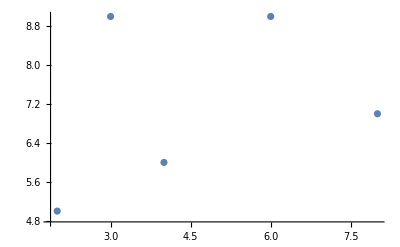

```mathematica
ListPlot[{{3,9},{4,6},{8,7},{6,9},{2,5}}]
```

### Задание 1.6 . Напишите булеву функцию, определяющую пересечение прямой и полигона.

```mathematica
isLineIntersectsPolygon[Polygon_kmPolygon,Line_kmLine]:=Module[{points=Polygon["coordsOfPoints"]},ContainsAny[(Line["equ"][[1]]/.{x->points[[#,1]],y->points[[#,2]]})>0&/@Range[Length@points],{True}]]
```

Проверяю

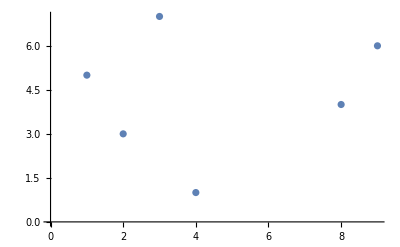

```mathematica
ListPlot[{{1,5},{2,3},{4,1},{8,4},{9,6},{3,7}}]
```

```mathematica
isLineIntersectsPolygon[Polygon5,kmLine[{kmPoint[{1,5}],kmPoint[{8,4}]}]]
```

True

### Задание 1.7 . Напишите функцию, вычисляющую взаимное положение полигона и прямой линии.

Варианты ответов : «прямая не пересекает полигон»; «прямая пересекает ребра полигона в < кол - во > точках, < список координат
точек пересечения > »; «прямая пересекает полигон по < кол - во > ребрам, < список ребер, т . е . список списков координат вершин ребра > » .

```mathematica
getLinePositionRelativePolygon[Polygon_kmPolygon,Line_kmLine]:=Module[{points=Polygon["coordsOfPoints"],dynamicTempValuesForCalculation={},dynamicPosForZeros,dynamicPosForOnes,res={},res1={}},
dynamicTempValuesForCalculation=(Line["equ"][[1]]/.{x->points[[#,1]],y->points[[#,2]]})&/@Range[Length@points];
dynamicPosForZeros=Position[dynamicTempValuesForCalculation,0];
If[dynamicPosForZeros!={},
dynamicPosForOnes=Position[Differences[dynamicPosForZeros],{1}];
If[dynamicPosForOnes!={},
res=First@First@AppendTo[res,{"Amount of intersected edges: " <> ToString[Length@dynamicPosForOnes] <> " with points " <> 
ToString[{points[[First@First@dynamicPosForZeros[[#]]]],points[[First@First@dynamicPosForZeros[[#]]+1]]}&/@dynamicPosForOnes]}],res=AppendTo[res,"There no edje intersections"]];
If[dynamicPosForOnes=={},None,dynamicPosForZeros=Delete[dynamicPosForZeros,Flatten[{{{First@#},{First@#+1}}&/@dynamicPosForOnes},2]]];
If[Or[dynamicPosForZeros=={{}},dynamicPosForZeros=={}],res,
res1=AppendTo[res1,"amount of intersected vertices: " <> ToString[Length@First@dynamicPosForZeros] <> " with points " <> 
ToString[(points[[#]]&/@(dynamicPosForZeros))]]],
False];
If[ToString@res=="{}",res1,If[ToString@res1=="{}",res,res<>", "<>res1]]]
```

```mathematica
Polygon8=kmPolygon[{{1,2},{1,1},{5,1},{5,10},{1,8},{3,6},{1,5},{1,4},{3,3}}]
```

Polygon: (,,{1,2}{1,1}{5,1}{5,10}{1,8}{3,6}{1,5}{1,4}{3,3})

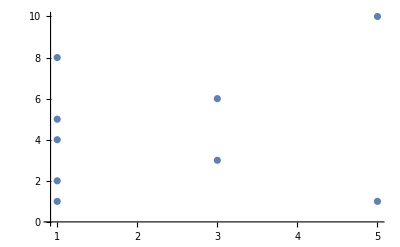

```mathematica
ListPlot[{{1,2},{1,1},{5,1},{5,10},{1,8},{3,6},{1,5},{1,4},{3,3}}]
```

```mathematica
getLinePositionRelativePolygon[Polygon8,kmLine[{kmPoint[{1,1}],kmPoint[{1,8}]}]]
```

Amount of intersected edges: 2 with points {{{1, 2}, {1, 1}}, {{1, 5}, {1, 4}}}, amount of intersected vertices: 1 with points {{{1, 8}}}

```mathematica
getLinePositionRelativePolygon[Polygon5,kmLine[{kmPoint[{1,5}],kmPoint[{8,4}]}]]
```

There no edje intersections, amount of intersected vertices: 1 with points {{{1, 5}}, {{8, 4}}}

```mathematica
getLinePositionRelativePolygon[Polygon5,kmLine[{kmPoint[{1,5}],kmPoint[{2,3}]}]]
```

Amount of intersected edges: 1 with points {{{1, 5}, {2, 3}}}